```mathematica
Monitor[Table[Table[CalcVotedValuesSummaryForRangePure[Reverse[Subsets[Prime[Range[last,last+l-1]], {l}]], range], {last,2,100}, {range,40001,5001,-5000}], {l,4,4}],ToString[l] <> " - " <> ToString[last] <> " - " <> ToString[ Prime[last]]<> " - " <> ToString[ range]]
```

$Aborted

```mathematica
Prime[50]
```

229

```mathematica
Streams[]
```

{OutputStream[stdout,1],OutputStream[stderr,2]}

```mathematica
Close[Streams[][[3]]]
```

d:\Triangle\Votes\Summary\VotedValuesAtHeight-40000.txt

```mathematica
Length[Subsets[Prime[Range[2,20]], {7}]]
```

50388

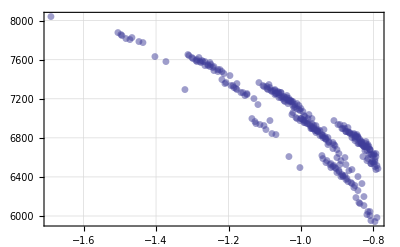

```mathematica
With[
{range = 16000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
ListPlot[
Sort[Table[N [{magicGraham[tuple[[1]]],Log[tuple[[2]]]}], {tuple, values}]],
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1200},
PlotRange->All,
PlotStyle->Opacity[0.5]
] 
]
]
]
```

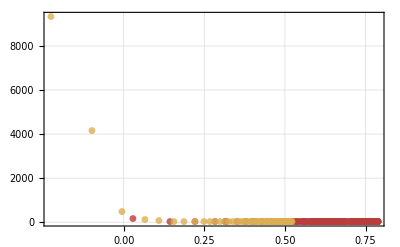

```mathematica
With[
{range = 40000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
Monitor[
Show[
Table[
ListPlot[
Sort[Table[N [{magicGraham[tuple[[1]]],Log[tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]]==l&]}]],
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1200},
PlotRange->All,
PlotStyle->{Opacity[0.8], ColorData["DarkRainbow"][1/(Log[l])]}
] 
,{l,2,Max[Map[Length[#[[1]]]&, values]]}]
],
tuple[[1]]
]
]
]
]
```

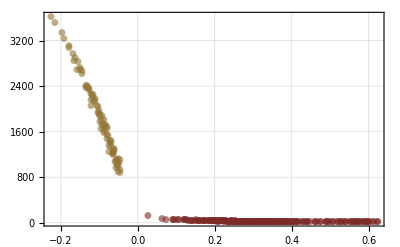

```mathematica
With[
{range = 16000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
Monitor[
Show[
Table[
ListPlot[
Sort[Table[N [{magicGraham[tuple[[1]]],Log[tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]]==l&]}]],
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1200},
PlotRange->All,
PlotStyle->{Opacity[0.6], Darker[ColorData["DarkRainbow"][1/(Log[l])]]}
] 
,{l,Min[Map[Length[#[[1]]]&, values]],Max[Map[Length[#[[1]]]&, values]]}]
],
tuple[[1]]
]
]
]
]
```

```mathematica
Select[ReadList[FileNameForVotedValuesSummary[1000]], Length[#[[1]]]==2&]
```

{{{3,5},14535650},{{3,7},14375965},{{3,11},708624},{{3,13},774442},{{3,17},590825},{{3,19},789588},{{3,23},1680710},{{3,29},245061},{{3,31},1851048},{{3,37},265680},{{5,7},876525},{{5,11},397138},{{5,13},407151},{{5,17},100310},{{5,19},179550},{{5,23},113257},{{5,29},109535},{{5,31},101380},{{5,37},116930},{{7,11},352970},{{7,13},154158},{{7,17},123235},{{7,19},55735},{{7,23},53568},{{7,29},56414},{{7,31},123140},{{7,37},55329},{{11,13},175978},{{11,17},35964},{{11,19},44175},{{11,23},61600},{{11,29},36570},{{11,31},36587},{{11,37},21916},{{13,17},40601},{{13,19},37603},{{13,23},42424},{{13,29},31294},{{13,31},31839},{{13,37},58141},{{17,19},30382},{{17,23},26708},{{17,29},26918},{{17,31},31010},{{17,37},16852},{{19,23},29627},{{19,29},30363},{{19,31},30857},{{19,37},15621},{{23,29},28107},{{23,31},36619},{{23,37},16468},{{29,31},32896},{{29,37},11109},{{31,37},12580},{{3,41},552109},{{5,41},84510},{{7,41},34450},{{11,41},30630},{{13,41},30761},{{17,41},15712},{{19,41},17066},{{23,41},17186},{{29,41},10423},{{31,41},11787},{{37,41},12360},{{3,43},197896},{{5,43},81533},{{7,43},34114},{{11,43},32219},{{13,43},31490},{{17,43},17175},{{19,43},17050},{{23,43},17077},{{29,43},11283},{{31,43},11671},{{37,43},11180},{{41,43},17056},{{3,47},243524},{{5,47},110933},{{7,47},51475},{{11,47},29672},{{13,47},9376},{{17,47},20033},{{19,47},15944},{{23,47},17719},{{29,47},11327},{{31,47},11571},{{37,47},11327},{{41,47},11950},{{43,47},11533}}

```mathematica
N[Log[10,17507351252391052043707559246991781537802847497633126463135380892521240645414785263874205575287826587305910275390450686009953917786327416268837218118896902757868713215594674009566354084793942548108079441671473602832075325048553035185646863604957829070477489996642225421185670116840940385001774373742411004502192492204204322242223775682488266269090114817941720833128511162720515427789756054995524815183484236017116234226905953370322032821554253311697235207411865226724822870466576460512687715307523760712575385628513554025071509887826463329507307336046554772156704728290965144809417796113186149479438684219785022054756801998469990618938662954526347014208879105397750145550419414587391213887925081908777950774064855634465358697555874295634842959991956846068612912933151102627472713606981681123451783669720796600360449392556801093995588961820245743402060832185454669547935876703049755005403694739541836227314883426931841366161563003502709742590094670792740392095317936376823414280321084767460299110076847717904201205049805644934218756039937902789408011737959409538792050584689600616888680017333651638150459100891934716859801944559065841924385434772053882444605052627407440143933177866670707091066726542119838418669240038637952030170823114753657790514294093065123351448000595800897560625845345542491353579972944334672994706864544728266985299085383704809371406097525221519821058306987900472279980649974702615221824929626271271807873780180295573577042676458370205219431519099021523467560552414175733964882143963197647363936012867075900068138784864698236657644570073148634435973379850476329264930597700105932489631521014765165901804421812936923093889005646076863019348134825963621082374297139493826546548132188816330126216973230284365084571869119318489796268740031228518765625101586809607323370788653165782829003651641702004197608175345934061285072601290779883915622835659797469308572350321833064468056470472286999035298981349294906740270742142796056625586734877314967705370795014284190768025023167271206835287310903546742116693409469813005175447648121727072521186275548397492111728375621975881310429323725732519087900580370278099370236270750454061215891505690700592504234476580632808086769223661126485555278236023474211369393659736310716408476829309413078839803788948834936242722627243735036970107427344384963570163076380127551259195282500232874685284710605948338570080350711494586148537160776844891687251245750710350304103581134323283605713574459252433610118899116834221283212989844358065931926388590238834383674091129993739412311891114888099680960116975467220653199467431091703015753585771470197949559413535773242978690016297971936644406442154922303760766311457805700764781484197469231225939]]
```

2686.24

```mathematica
a=Map[{#, MultiplyDigits[#]}&,Map[First[#]&,ReadList[FileNameForVotedValuesSummary[1000]]]]
```

{{{3,5},15},{{3,7},21},{{3,11},33},{{3,13},39},{{3,17},51},{{3,19},57},{{3,23},69},{{3,29},87},{{3,31},93},{{3,37},111},{{5,7},35},{{5,11},55},{{5,13},65},{{5,17},85},{{5,19},95},{{5,23},115},{{5,29},145},{{5,31},155},{{5,37},185},{{7,11},77},{{7,13},91},{{7,17},119},«11781»,{{11,13,17,19,41,47},89006203},{{11,13,17,19,43,47},93347969},{{11,13,17,23,29,47},76209419},{{11,13,17,23,31,47},81465241},{{11,13,17,23,37,47},97232707},{{11,13,17,23,41,47},107744351},{{11,13,17,23,43,47},113000173},{{11,13,17,29,31,47},102717043},{{11,13,17,29,37,47},122597761},{{11,13,17,29,41,47},135851573},{{11,13,17,29,43,47},142478479},{{11,13,17,31,37,47},131052779},{{11,13,17,31,41,47},145220647},{{11,13,17,31,43,47},152304581},{{11,13,17,37,41,47},173327869},{{11,13,17,37,43,47},181782887},{{11,13,17,41,43,47},201435091},{{11,13,19,23,29,47},85175233},{{11,13,19,23,31,47},91049387},{{11,13,19,23,37,47},108671849},{{11,13,19,23,41,47},120420157}}

```mathematica
Norm[ {2, 5,7}]
```

√78

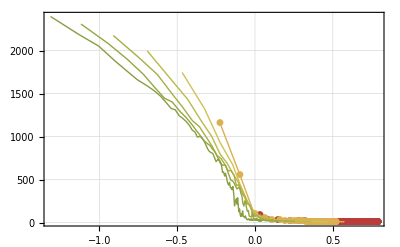

```mathematica
With[
{range = 5000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
Monitor[
Show[
Table[
ListLinePlot[
Sort[Table[N [{magicGraham[tuple[[1]]],Log[tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]]==l&]}]],
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1200},
PlotRange->All,
PlotStyle->{Opacity[1], ColorData["DarkRainbow"][1/(Log[l])]}
] 
,{l,Min[Map[Length[#[[1]]]&, values]],Max[Map[Length[#[[1]]]&, values]]}]
],
tuple[[1]]
]
]
]
]
```

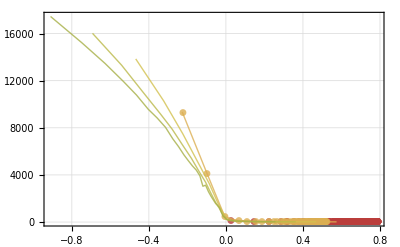

```mathematica
With[
{range = 40000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
Monitor[
Show[
Table[
ListLinePlot[
Sort[Table[N [{magicGraham[tuple[[1]]],Log[tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]]==l&]}]],
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1200},
PlotRange->All,
PlotStyle->{Opacity[0.8], ColorData["DarkRainbow"][1/(Log[l])]}
] 
,{l,Min[Map[Length[#[[1]]]&, values]],7}]
],
tuple[[1]]
]
]
]
]
```

```mathematica
N[Exp[20000]]
```

7.756004726×10^8685

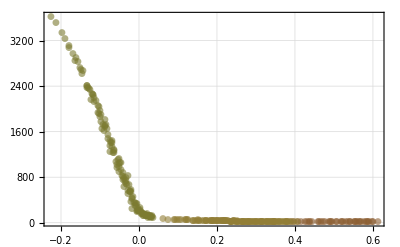

```mathematica
With[
{range = 16000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
With [
{start=Min[Map[Length[#[[1]]]&, values]], end=Max[Map[Length[#[[1]]]&, values]]},
Monitor[
Show[
Table[
ListPlot[
Sort[Table[N [{magicGraham[tuple[[1]]],Log[tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]]==l&]}]],
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1200},
PlotRange->All,
PlotStyle->{Opacity[0.6], Darker[ColorData["DarkRainbow"][1-(l / (end -start+1))]]}
] 
,{l,start,end}]
],
tuple[[1]]
]
]
]
]
]
```